```mathematica
SetDirectory["/home/s1220054/Dissertation/Dissertation/DiSamp/src"]
```

/home/s1220054/Dissertation/Dissertation/DiSamp/src

```mathematica
data = Import["phidist.txt","CSV"]
```

{{0,0.000197433},{1,0},{2,0.000789733},{3,0.000394867},{4,0.000789733},{5,0.000987167},{6,0.000987167},{7,0.0017769},{8,0.00276407},{9,0.000987167},{10,0.00197433},{11,0.0017769},{12,0.00138203},{13,0.00375123},{14,0.0023692},{15,0.0035538},{16,0.00315893},{17,0.0041461},{18,0.00375123},{19,0.00276407},{20,0.00256663},{21,0.00375123},{22,0.00335637},{23,0.00394867},{24,0.00335637},{25,0.00375123},{26,0.00335637},{27,0.0035538},{28,0.0035538},{29,0.00375123},{30,0.00631787},{31,0.0035538},{32,0.0041461},{33,0.0035538},{34,0.00394867},{35,0.0041461},{36,0.00335637},{37,0.00335637},{38,0.00552813},{39,0.00493583},{40,0.00375123},{41,0.00513327},{42,0.00631787},{43,0.00691017},{44,0.005923},{45,0.005923},{46,0.00671273},{47,0.00671273},{48,0.00809477},{49,0.00691017},{50,0.00513327},{51,0.005923},{52,0.00730503},{53,0.00848963},{54,0.0065153},{55,0.00868707},{56,0.00631787},{57,0.00572557},{58,0.00789733},{59,0.0082922},{60,0.00789733},{61,0.00572557},{62,0.00750247},{63,0.00513327},{64,0.0082922},{65,0.00394867},{66,0.0047384},{67,0.0076999},{68,0.00809477},{69,0.0071076},{70,0.0071076},{71,0.00750247},{72,0.0102665},{73,0.0088845},{74,0.0047384},{75,0.00671273},{76,0.00671273},{77,0.0071076},{78,0.00493583},{79,0.0065153},{80,0.0082922},{81,0.0082922},{82,0.00671273},{83,0.00631787},{84,0.0065153},{85,0.0088845},{86,0.0102665},{87,0.00671273},{88,0.00908193},{89,0.0065153},{90,0.00789733},{91,0.00868707},{92,0.0076999},{93,0.00691017},{94,0.00750247},{95,0.00868707},{96,0.0071076},{97,0.00868707},{98,0.00631787},{99,0.00789733},{100,0.00671273},{101,0.0071076},{102,0.005923},{103,0.00612043},{104,0.0076999},{105,0.00750247},{106,0.00750247},{107,0.0065153},{108,0.00454097},{109,0.00789733},{110,0.0041461},{111,0.0065153},{112,0.00848963},{113,0.00809477},{114,0.00691017},{115,0.00572557},{116,0.00434353},{117,0.00631787},{118,0.00513327},{119,0.00671273},{120,0.00434353},{121,0.005923},{122,0.00671273},{123,0.0047384},{124,0.0035538},{125,0.0071076},{126,0.0053307},{127,0.00552813},{128,0.00434353},{129,0.005923},{130,0.00572557},{131,0.00493583},{132,0.00375123},{133,0.0053307},{134,0.00493583},{135,0.00572557},{136,0.00612043},{137,0.0047384},{138,0.00671273},{139,0.00434353},{140,0.00434353},{141,0.0047384},{142,0.00493583},{143,0.00434353},{144,0.00513327},{145,0.00552813},{146,0.0041461},{147,0.00493583},{148,0.00493583},{149,0.00454097},{150,0.0035538},{151,0.00335637},{152,0.00454097},{153,0.00493583},{154,0.00513327},{155,0.00375123},{156,0.0041461},{157,0.00217177},{158,0.00454097},{159,0.005923},{160,0.00454097},{161,0.0023692},{162,0.00394867},{163,0.00434353},{164,0.00315893},{165,0.0017769},{166,0.0053307},{167,0.0023692},{168,0.0023692},{169,0.0017769},{170,0.00256663},{171,0.0035538},{172,0.00335637},{173,0.00197433},{174,0.00315893},{175,0.00335637},{176,0.0029615},{177,0.00138203},{178,0.00315893},{179,0.0029615},{180,0.0029615},{181,0.0005923},{182,0.0017769},{183,0.00217177},{184,0.0029615},{185,0.00276407},{186,0.0023692},{187,0.00217177},{188,0.00157947},{189,0.00157947},{190,0.00217177},{191,0.00138203},{192,0.00217177},{193,0.00197433},{194,0.00217177},{195,0.000987167},{196,0.0017769},{197,0.00197433},{198,0.0017769},{199,0.00138203},{200,0.00157947},{201,0.00157947},{202,0.000789733},{203,0.0011846},{204,0.000987167},{205,0.000789733},{206,0.0011846},{207,0.00217177},{208,0.000789733},{209,0.0005923},{210,0.0005923},{211,0.0005923},{212,0.0011846},{213,0.0011846},{214,0.000789733},{215,0.000789733},{216,0.0005923},{217,0.00138203},{218,0.000789733},{219,0.00197433},{220,0.0005923},{221,0.000789733},{222,0.000197433},{223,0.0005923},{224,0.0011846},{225,0.0011846},{226,0.000789733},{227,0.0005923},{228,0.000197433},{229,0.000394867},{230,0.000197433},{231,0.000789733},{232,0.000197433},{233,0.000789733},{234,0.000394867},{235,0},{236,0},{237,0.0005923},{238,0.000197433},{239,0.000197433},{240,0.000197433},{241,0.000197433},{242,0},{243,0.000197433},{244,0.000394867},{245,0.000987167},{246,0.000197433},{247,0.0005923},{248,0},{249,0.000197433},{250,0},{251,0.000197433},{252,0},{253,0.000197433},{254,0.000197433},{255,0},{256,0},{257,0},{258,0},{259,0},{260,0},{261,0},{262,0.000197433},{263,0},{264,0},{265,0},{266,0},{267,0},{268,0},{269,0},{270,0},{271,0},{272,0},{273,0},{274,0},{275,0},{276,0},{277,0},{278,0},{279,0},{280,0},{281,0},{282,0},{283,0},{284,0},{285,0},{286,0},{287,0},{288,0},{289,0},{290,0},{291,0},{292,0},{293,0},{294,0},{295,0},{296,0},{297,0},{298,0},{299,0},{300,0},{301,0},{302,0},{303,0},{304,0},{305,0},{306,0},{307,0},{308,0},{309,0},{310,0},{311,0},{312,0},{313,0},{314,0},{315,0},{316,0},{317,0},{318,0},{319,0},{320,0},{321,0},{322,0},{323,0},{324,0},{325,0},{326,0},{327,0},{328,0},{329,0},{330,0},{331,0},{332,0},{333,0},{334,0},{335,0},{336,0},{337,0},{338,0},{339,0},{340,0},{341,0},{342,0},{343,0},{344,0},{345,0},{346,0},{347,0},{348,0},{349,0},{350,0},{351,0},{352,0},{353,0},{354,0},{355,0},{356,0},{357,0},{358,0},{359,0},{360,0},{361,0},{362,0},{363,0},{364,0},{365,0},{366,0},{367,0},{368,0},{369,0},{370,0},{371,0},{372,0},{373,0},{374,0},{375,0},{376,0},{377,0},{378,0},{379,0},{380,0},{381,0},{382,0},{383,0},{384,0},{385,0},{386,0},{387,0},{388,0},{389,0},{390,0},{391,0},{392,0},{393,0},{394,0},{395,0},{396,0},{397,0},{398,0},{399,0},{400,0},{401,0},{402,0},{403,0},{404,0},{405,0},{406,0},{407,0},{408,0},{409,0},{410,0},{411,0},{412,0},{413,0},{414,0},{415,0},{416,0},{417,0},{418,0},{419,0},{420,0},{421,0},{422,0},{423,0},{424,0},{425,0},{426,0},{427,0},{428,0},{429,0},{430,0},{431,0},{432,0},{433,0},{434,0},{435,0},{436,0},{437,0},{438,0},{439,0},{440,0},{441,0},{442,0},{443,0},{444,0},{445,0},{446,0},{447,0},{448,0},{449,0},{450,0},{451,0},{452,0},{453,0},{454,0},{455,0},{456,0},{457,0},{458,0},{459,0},{460,0},{461,0},{462,0},{463,0},{464,0},{465,0},{466,0},{467,0},{468,0},{469,0},{470,0},{471,0},{472,0},{473,0},{474,0},{475,0},{476,0},{477,0},{478,0},{479,0},{480,0},{481,0},{482,0},{483,0},{484,0},{485,0},{486,0},{487,0},{488,0},{489,0},{490,0},{491,0},{492,0},{493,0},{494,0},{495,0},{496,0},{497,0},{498,0},{499,0},{500,0},{501,0},{502,0},{503,0},{504,0},{505,0},{506,0},{507,0},{508,0},{509,0},{510,0},{511,0},{512,0},{513,0},{514,0},{515,0},{516,0},{517,0},{518,0},{519,0},{520,0},{521,0},{522,0},{523,0},{524,0},{525,0},{526,0},{527,0},{528,0},{529,0},{530,0},{531,0},{532,0},{533,0},{534,0},{535,0},{536,0},{537,0},{538,0},{539,0},{540,0},{541,0},{542,0},{543,0},{544,0},{545,0},{546,0},{547,0},{548,0},{549,0},{550,0},{551,0},{552,0},{553,0},{554,0},{555,0},{556,0},{557,0},{558,0},{559,0},{560,0},{561,0},{562,0},{563,0},{564,0},{565,0},{566,0},{567,0},{568,0},{569,0},{570,0},{571,0},{572,0},{573,0},{574,0},{575,0},{576,0},{577,0},{578,0},{579,0},{580,0},{581,0},{582,0},{583,0},{584,0},{585,0},{586,0},{587,0},{588,0},{589,0},{590,0},{591,0},{592,0},{593,0},{594,0},{595,0},{596,0},{597,0},{598,0},{599,0},{600,0},{601,0},{602,0},{603,0},{604,0},{605,0},{606,0},{607,0},{608,0},{609,0},{610,0},{611,0},{612,0},{613,0},{614,0},{615,0},{616,0},{617,0},{618,0},{619,0},{620,0},{621,0},{622,0},{623,0},{624,0},{625,0},{626,0},{627,0},{628,0},{629,0},{630,0},{631,0},{632,0},{633,0},{634,0},{635,0},{636,0},{637,0},{638,0},{639,0},{640,0},{641,0},{642,0},{643,0},{644,0},{645,0},{646,0},{647,0},{648,0},{649,0},{650,0},{651,0},{652,0},{653,0},{654,0},{655,0},{656,0},{657,0},{658,0},{659,0},{660,0},{661,0},{662,0},{663,0},{664,0},{665,0},{666,0},{667,0},{668,0},{669,0},{670,0},{671,0},{672,0},{673,0},{674,0},{675,0},{676,0},{677,0},{678,0},{679,0},{680,0},{681,0},{682,0},{683,0},{684,0},{685,0},{686,0},{687,0},{688,0},{689,0},{690,0},{691,0},{692,0},{693,0},{694,0},{695,0},{696,0},{697,0},{698,0},{699,0},{700,0},{701,0},{702,0},{703,0},{704,0},{705,0},{706,0},{707,0},{708,0},{709,0},{710,0},{711,0},{712,0},{713,0},{714,0},{715,0},{716,0},{717,0},{718,0},{719,0},{720,0},{721,0},{722,0},{723,0},{724,0},{725,0},{726,0},{727,0},{728,0},{729,0},{730,0},{731,0},{732,0},{733,0},{734,0},{735,0},{736,0},{737,0},{738,0},{739,0},{740,0},{741,0},{742,0},{743,0},{744,0},{745,0},{746,0},{747,0},{748,0},{749,0},{750,0},{751,0},{752,0},{753,0},{754,0},{755,0},{756,0},{757,0},{758,0},{759,0},{760,0},{761,0},{762,0},{763,0},{764,0},{765,0},{766,0},{767,0},{768,0},{769,0},{770,0},{771,0},{772,0},{773,0},{774,0},{775,0},{776,0},{777,0},{778,0},{779,0},{780,0},{781,0},{782,0},{783,0},{784,0},{785,0},{786,0},{787,0},{788,0},{789,0},{790,0},{791,0},{792,0},{793,0},{794,0},{795,0},{796,0},{797,0},{798,0},{799,0},{800,0},{801,0},{802,0},{803,0},{804,0},{805,0},{806,0},{807,0},{808,0},{809,0},{810,0},{811,0},{812,0},{813,0},{814,0},{815,0},{816,0},{817,0},{818,0},{819,0},{820,0},{821,0},{822,0},{823,0},{824,0},{825,0},{826,0},{827,0},{828,0},{829,0},{830,0},{831,0},{832,0},{833,0},{834,0},{835,0},{836,0},{837,0},{838,0},{839,0},{840,0},{841,0},{842,0},{843,0},{844,0},{845,0},{846,0},{847,0},{848,0},{849,0},{850,0},{851,0},{852,0},{853,0},{854,0},{855,0},{856,0},{857,0},{858,0},{859,0},{860,0},{861,0},{862,0},{863,0},{864,0},{865,0},{866,0},{867,0},{868,0},{869,0},{870,0},{871,0},{872,0},{873,0},{874,0},{875,0},{876,0},{877,0},{878,0},{879,0},{880,0},{881,0},{882,0},{883,0},{884,0},{885,0},{886,0},{887,0},{888,0},{889,0},{890,0},{891,0},{892,0},{893,0},{894,0},{895,0},{896,0},{897,0},{898,0},{899,0},{900,0}}

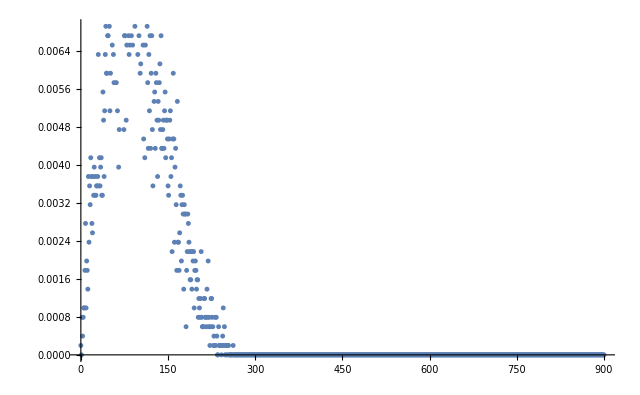

```mathematica
ListPlot[data]
```

```mathematica
data2 = Import["new.txt","CSV"]
```

{{214,278},{214,280},{214,281},{214,282},{215,277},{215,278},{215,279},{215,280},{215,281},{215,282},{215,283},{215,285},{215,286},{215,287},{215,288},{215,289},{215,292},{215,295},19556,{389,294},{389,295},{389,296},{389,297},{389,298},{389,299},{389,300},{389,301},{389,302},{390,293},{390,294},{390,295},{390,296},{390,297},{390,298},{390,299},{390,300},{391,296}}
 |  |  |  |

```mathematica
data3 = Import["type2.txt","CSV"]
```

{{211,292},{211,293},{211,302},{212,291},{212,292},{212,293},{212,294},{212,295},{212,297},{212,298},{212,299},{212,300},{212,301},{212,302},{212,303},{212,304},{213,290},{213,291},15967,{389,334},{389,335},{389,336},{389,337},{389,338},{389,339},{389,340},{389,341},{389,342},{389,344},{389,345},{389,346},{390,324},{390,325},{390,326},{390,328},{391,325},{391,326}}
 |  |  |  |

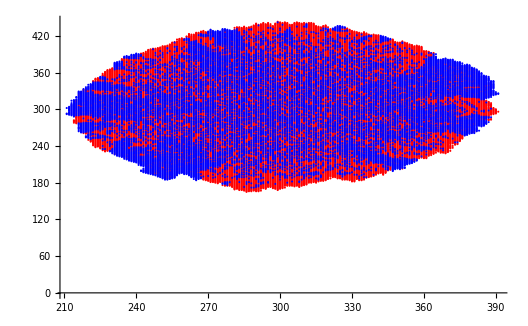

```mathematica
ListPlot[{data2,data3},PlotStyle->{Red,Blue}]
```